```mathematica
(*Ecuaciones en el equilibrio de C0 a C5 y S (llamada aquí C6)*)
ecuac={
0==kon Peq*Teq-(koff+kp) C0+(b+γ (a*C1*ST)/(a*C1+1)) C1,
0==kp C0-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C1+(b+γ (a*C1*ST)/(a*C1+1)) C2,
0==kp C1-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C2+(b+γ (a*C1*ST)/(a*C1+1)) C3,
0==kp C2-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C3+(b+γ (a*C1*ST)/(a*C1+1)) C4,
0==kp C3-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C4+(b+γ (a*C1*ST)/(a*C1+1)) C5,
0==kp C4-(koff+b+γ (a*C1*ST)/(a*C1+1)) C5
}//.γ (a*C1*ST)/(a*C1+1)->C6;
sept={0==C6(a*C1+1)-γ a*C1*ST};
ecuaciones=Join[ecuac,sept];
TableForm[ecuaciones]
```

0==C1 (b+C6)-C0 (koff+kp)+kon Peq Teq
0==C2 (b+C6)+C0 kp-C1 (b+C6+koff+kp)
0==C3 (b+C6)+C1 kp-C2 (b+C6+koff+kp)
0==C4 (b+C6)+C2 kp-C3 (b+C6+koff+kp)
0==C5 (b+C6)+C3 kp-C4 (b+C6+koff+kp)
0==-C5 (b+C6+koff)+C4 kp
0==(1+a C1) C6-a C1 ST γ

```mathematica
(*Solución simbólica de C0 a C6 en el equilibrio*)
soluc=Solve[ecuaciones,{C0,C1,C2,C3,C4,C5,C6}];
Length[soluc]
```

6

```mathematica
specificC5=C5/. soluc[[2]];
simplifiedSpecificC5=Simplify[specificC5];
(*TeXForm[simplifiedSpecificC5]*)
```

```mathematica
parametersFull={kon->1/10^5,koff->0.05,kp->0.09,b->0.04,γ->1/10^6, TT-> 3 10^4,ST->6 10^5,a->1/(5 10^2)};
(*Solución de P y T en el equilibrio*)
Clear[PT,TT]
Clear[Peq,Teq]
solPyT=Solve[{0==-kon Peq Teq+koff (PT-Peq),0==-kon Peq Teq+koff (TT-Teq)},{Peq,Teq}][[2]];
(*parámetros con Peq y Teq*)
parametrosconPeqyTeq=Join[parametersFull,solPyT//.parametersFull];
```

```mathematica
(*comprobación de que la solución 2 es la única Real y positiva*)
i=2;
solsC5=soluc[[i,6,2]]//.parametrosconPeqyTeq;
i=.
```

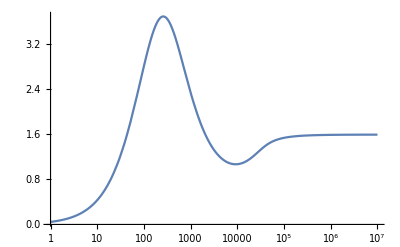

```mathematica
(*definición de C5 en el equilibrio en función de PT*)
C5eqLTT[x_]:=solsC5/.PT->x
(*gráfica de C5 en el equilibrio en función de PT*)
LogLinearPlot[C5eqLTT[LT],{LT,1,10^7},PlotRange->All]
```